# Building WolframCloud APIs for JavaScript (React, Node, AWS) Livecoding Session 4

## Initializations

https://www.wolframcloud.com/
https://datadrop.wolframcloud.com/

```mathematica
$CloudBase="https://www.wolframcloud.com/"
```

https://www.wolframcloud.com/

```mathematica
(*CloudConnect["...your account email..."]*)
CloudConnect["mitch@aitoconsulting.com"]
```

mitch@aitoconsulting.com

```mathematica
ClearAll[choices,get]
choices=Sort[{"posts","comments","albums","photos","todos","users"}]
get[it_String]:=Import["https://jsonplaceholder.typicode.com/"<>it,"RawJSON"]
```

{albums,comments,photos,posts,todos,users}

## Overview

Assumptions:
- Familiarity with Mathematica.  
- Familiarity of JS is helpful but not required for this presentation.

A few words about:
- Introduction and background for React (https://reactjs.org/) / Axios and Node (https://nodejs.org/en/) / Express.
- Wolfram setup, we will use the following tools:
	- Mathematica desktop (wolfram.com/) & Wolfram Cloud (wolframcloud.com - free sign up.  You can use Wolfram Cloud (WC) alone if you like)
- Other than Wolfram setup:
	- npm (https://www.npmjs.com/) 
	- git (https://git-scm.com/)
	- GitHub (https://github.com/)
	- AWS (free tier: https://aws.amazon.com/console/)
	- AWS-CLI (https://aws.amazon.com/cli/)
	- AWS Amplify (https://aws.amazon.com/amplify/)
	- create-react-app (https://facebook.github.io/create-react-app/)
	- Chrome browser (google.com/chrome).  We will use chrome developer tools.  Other browsers and their browser tools may not be sufficient for what we will doing)
	- Postman (getpostman.com/ for validating and testing APIs)

## Introduction

Motivating principle: separation of duties for people and software supporting the goals of modular design principles.  Easy to understand separating people by expertise in front-end, back-end and quantitative capabilities and code production.

This is the first of three (or more) live-coding walk-through’s that show an approach to integrating Mathematica to a browser front-end (ReactJS) and a serverless back-end (Node JS and AWS).

ReactJS is a JavaScript (JS) library widely used to make single page applications (SPAs).   ‘Hooks’ were introduced in the recently released version 16.8 (https://reactjs.org/docs/hooks-intro.html).  Using hooks allows React developers to write JS applications using 100% functional methods - eliminating the need for JS classes.  There are many advantages to this new capability and we will focus on the implications for APIs between React and the Wolfram Cloud (WC) and between AWS and WC.

We will show JS and JSX (https://reactjs.org/docs/introducing-jsx.html) with respect to how the API requests (req) and responses (res) are managed.  The JS browser app is a bear bones deployment with minimal styling and organization considerations.  

We will iterate from the simplest possible API (that I can think of) to ever more complex patterns.  There are JS and React considerations that impact the WC side of the API.  A number of these considerations will be presented, discussed and dealt with.  In every instance the goal is to produce Mathematica side code that is simultaneously used for presentation in a browser and analytical use is Mathematica. 

Some requests and considerations:
- You will see the URL I use (my WC account) and API end-points I am using.  I've made these public for these live coding sessions.  It's ok during the live coding session to use my APIs if you can't make yours work, but please setup your own WC account, make your own APIs and use them.

The general development pattern:
1.0) Three parts to APIFunction[...]:
	1.1) inputs
	1.2) functions
	1.3) output format
2.0) Test by passing an association of API inputs <|key -> value, ...|>
3.0) Two’ish parts to CloudDeploy[...]:
	3.1) the api function (1 above)
	3.2) options:
		3.2.1) the path and api name
		3.2.2) permissions
4.0) Test:
	4.1) to a browser with StartWebSession[...] and WebExecute[...]
	4.2) to postman
5.0) Connect to:
	5.1) front-end (React)
	5.2) backend (Node)
		5.2.1) test serverless api between AWS (via Node) and WC 

Here are a couple web sites that are built on this pattern where the front-end is a Single Page Application (SPA) using React, the back-end is serverless and built on NodeJS - AWS, and everything computational is done with Wolfram (Wolfram Cloud):
	- https://www.aitoconsulting.org/options-pub
	- https://www.christyhealth.org/

## Build your own API maker functions : v01

```mathematica
ClearAll[makeAPI,args,func,frmt]
makeAPI[args_List, func_Function,frmt_String]:= APIFunction[
args,
func,
 frmt
];

ClearAll[makeCD,args,func,frmt]
makeCD[args_List, func_Function,frmt_String,endPoint_String,funcName_String,permit_String]:=CloudDeploy[
makeAPI[args, func,frmt],
"/"<>endPoint<>"/"<>funcName<>"/",
Permissions->"Public"
];
```

```mathematica
ClearAll[args,func,frmt,params]
args={"x"->Interpreter["Integer"],"y"->Interpreter["Integer"]};
func=Function[ RandomInteger[{#x,#y}] ];
frmt="JSON";

params=<|"x"->-10,"y"->10|>;
makeAPI[args, func,frmt][params]
```

-2

```mathematica
endPoint="live-coding-unitTest";
funcName="random-integer";
permit="Public";

makeCD[args, func,frmt,endPoint,funcName,permit]
```

CloudObject[https://www.wolframcloud.com/obj/mitch/live-coding-unitTest/random-integer]

## API - 10) Images - Getting size and aspect ratio ‘right’

On to Images...

### Back to making APIs (for <img /> tags)

With the basics out of the way let’s get back to making APIs.  We’ll use Solve[ ] to produce a couple equations then make an image of the result and return it via an API.

Note the interaction between font size, image size and aspect ratio.

Comment: 
make sure to load custom functions used in the Function block into kernel memory before evaluating APIFunction[ ].  Or, add the custom function into the Function block.

Really helpful tip:
don’t send Symbols to HTML!  Replace them with Strings.
/. is shorthand for ReplaceAll[...]

```mathematica
ClearAll[eq,x,a]
eq=Solve[x^2+a x+1==0,x];
eq//Head
%%//FullForm
eq/.{x->"x",a->"a"}
%//FullForm
```

List

List[List[Rule[x,Times[Rational[1,2],Plus[Times[-1,a],Times[-1,Power[Plus[-4,Power[a,2]],Rational[1,2]]]]]]],List[Rule[x,Times[Rational[1,2],Plus[Times[-1,a],Power[Plus[-4,Power[a,2]],Rational[1,2]]]]]]]

{{x→1/2 (-a-√(-4+a^2))},{x→1/2 (-a+√(-4+a^2))}}

List[List[Rule["x",Times[Rational[1,2],Plus[Times[-1,"a"],Times[-1,Power[Plus[-4,Power["a",2]],Rational[1,2]]]]]]],List[Rule["x",Times[Rational[1,2],Plus[Times[-1,"a"],Power[Plus[-4,Power["a",2]],Rational[1,2]]]]]]]

```mathematica
ClearAll[grd,rstr,bpW,w,h,xL,xR,yT,yC,yB,fs,rsMult]
xL=0;
xR=0;
yT=0;
yC=1;
yB=0;
bpW=200;(*base pixels width*)
w=16;
h=9;
fs=17.5;(*font size*)
rsMult=3;(*RasterSize multiple*)
```

```mathematica
(* makeAPI, makeCD, and WebExecute *)
ClearAll[args,func,frmt,params,endPoint,funcName,permit,url,session]
(* required custom functions *)
ClearAll[wPX,hPX,bp,w,h]
wPX[base_]:=base
wPX[base_,w_,h_]:=base*(w/h)//N
hPX[base_]:=base
hPX[base_,w_,h_]:=base*(h/w)//N

args={
"xL"->"Number",
"xR"->"Number",
"yT"->"Number",
"yC"->"Number",
"yB"->"Number",
"bpW"->"Number",
"w"->"Number",
"h"->"Number",
"fs"->"Number",
"rsMult"->"Number",
"gridFrame"->"Boolean",
"imageFrame"->"Boolean"
};
func=Function[
ClearAll[a,x];

Rasterize[
Framed[
Item[
Style[
Grid[

Solve[x^2+a x+1==0,x],

Spacings->{{#xL,#xR},{#yT,#yC,#yB}},
Frame->All,FrameStyle->If[#gridFrame,Gray,White]
],
FontFamily->"Arabic Transparent",FontSize->#fs
],
Alignment->{Center,Center}
],
ImageSize->{wPX[#bpW],hPX[#bpW,#w,#h]},
FrameMargins->{{0,0},{0,0}},
ContentPadding->False,
RoundingRadius->0,
FrameStyle->If[#imageFrame,Red,White]
],
ImageSize->{wPX[#bpW],hPX[#bpW,#w,#h]},
RasterSize->#rsMult*#bpW
]
];
frmt="PNG";
params=<|
"xL"->0,
"xR"->0,
"yT"->0,
"yC"->0,
"yB"->0,
"bpW"->200,
"w"->16,
"h"->9,
"fs"->17.5,
"rsMult"->3,
"gridFrame"->True,
"imageFrame"->True
|>;
endPoint="live-coding";
funcName="equation";
permit="Public";
```

```mathematica
makeAPI[args,func,frmt][params]
```

-Graphics-

```mathematica
makeCD[args, func,frmt,endPoint,funcName,permit]
```

CloudObject[https://www.wolframcloud.com/obj/mitch/live-coding/equation]

```mathematica
url=URLBuild[makeCD[args, func,frmt,endPoint,funcName,permit],params]
session=StartWebSession["Chrome"];
WebExecute[session,{"OpenPage"->url}];
```

https://www.wolframcloud.com/obj/mitch/live-coding/equation?xL=0&xR=0&yT=0&yC=0&yB=0&bpW=200&w=16&h=9&fs=17.5&rsMult=3&gridFrame=true&imageFrame=true

Let’s go to the JavaScript <img /> tag and play with width and height methods...

```mathematica
hPX[200,16,9]
```

112.5

```mathematica
hPX[400,21,9]
```

171.429

## API-11) Ways to return combinations of images and tables

#### Create DB

Make a data repository using Databin

```mathematica
(* CAUTION - running this cell will make a new Databin *)
(*
ClearAll[readingsDB]
readingsDB=CreateDatabin[<|"Name"->"readings",Permissions->"Public"|>]
*)

ClearAll[readingsDB]
readingsDB=CreateDatabin[<|"Name"->"readings",Permissions->"Public"|>]
```

Databin[…]

#### Get your databins

```mathematica
Databins[]
```

{Databin[…],Databin[…],Databin[…]}

#### Make Dataset[...] of databins

```mathematica
ClearAll[databinDS]
databinDS=Dataset[<|"shortID"-> #["ShortID"],"name"-> #["Name"],"databin"->#|>&/@Databins[]]
```

Dataset[<>]

```mathematica
ClearAll[readingsDB]
readingsDB=databinDS[Select[#name == "readings"&& #shortID=="FP1rDZCv"&],"databin"]//First
```

Databin[…]

```mathematica
ClearAll[readingsDS]
readingsDS=Dataset[readingsDB]
```

Dataset[<>]

#### Adding to a Databin

```mathematica
readingsDB=DatabinAdd[readingsDB,<|"reading"->RandomInteger[{0,100}]|>]
readingsDS=Dataset[readingsDB];
readingsDS[Union,All,Head]
readingsDS=Dataset[readingsDB][ReverseSortBy[#1,"AbsoluteTime"]&,{"Timestamp","reading"}]
```

Databin[…]

Dataset[<>]

Dataset[<>]

```mathematica
readingsDS[TimeSeries,{"Timestamp"/*DateString,"reading"}]
```

TimeSeries[…]

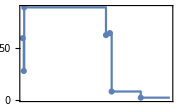

Graphics

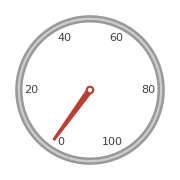

Graphics

```mathematica
dlsp=DateListStepPlot[readingsDS[TimeSeries,{"Timestamp"/*DateString,"reading"}],Right,Mesh->Full]
dlsp//Head
ag=AngularGauge[readingsDS[First,"reading"],{0,100},ImageSize->Small]
ag//Head
```

#### Mocking up...

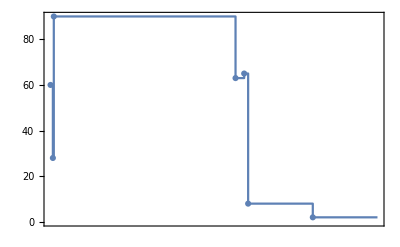
-Graphics- | Dataset[<>] | -Graphics-

```mathematica
Grid[{{ag,readingsDS[;;5],dlsp}},Frame->All,Alignment->Center]
```

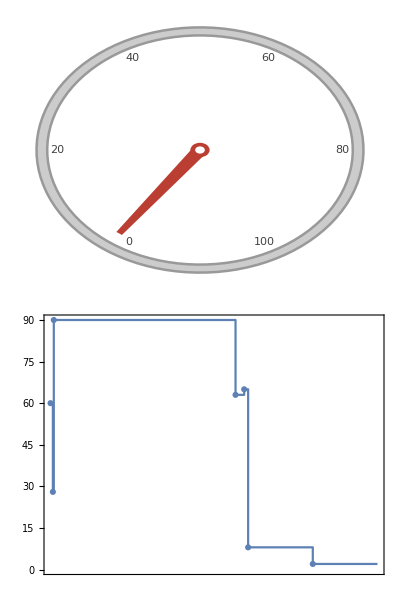
-Graphics- | Dataset[<>]

```mathematica
Grid[{{Column[{ag,dlsp}],readingsDS[;;10]}},Frame->All,Alignment->Center]
```

```mathematica
Column[{ag,dlsp,readingsDS[;;10]},Frame->All,Alignment->Center]
```

-Graphics-
-Graphics-
Dataset[<>]

```mathematica
readingsDS
```

Dataset[<>]

```mathematica
Normal[readingsDS[First,Keys,(Style[#,FontFamily->"Alegreya SC",FontSize->14,Bold]&)]]
```

{Timestamp,reading}

```mathematica
Join[
{Normal[readingsDS[First,Keys,(Style[#,FontFamily->"Alegreya SC",FontSize->14,Bold]&)]]},
Normal[readingsDS[;;3,Query[{"reading"/*(Style[#,FontFamily->"Arial",FontSize->8,Bold]&),"Timestamp"/*(Style[DateString[#],FontFamily->"Arial",FontSize->8,Bold]&)}]]]
]
```

{{Timestamp,reading},{2,Wed 14 Aug 2019 13:54:58},{8,Wed 14 Aug 2019 13:45:44},{65,Wed 14 Aug 2019 13:45:10}}

```mathematica
ClearAll[rows,grd]

grd[data_,rows_]:=Grid[
Join[
{Normal[data[First,Keys,(Style[#,FontFamily->"Alegreya SC",FontSize->14,Bold]&)]]},
Normal[data[;;rows,Query[{"reading"/*(Style[#,FontFamily->"Arial",FontSize->8,Bold]&),"Timestamp"/*(Style[DateString[#],FontFamily->"Arial",FontSize->8,Bold]&)}]]]
],
Background->{None,{1->LightBlue,Flatten[{1->LightBlue,#->Lighter[LightGray]&/@Range[3,rows+2,2]}]}},
Frame->All,
FrameStyle->Directive[LightGray],
Spacings->{{1,1,1},Table[.5,{(rows+2)}]}
];
grd[readingsDS,5]
%//Head
```

Timestamp | reading
2 | Wed 14 Aug 2019 13:54:58
8 | Wed 14 Aug 2019 13:45:44
65 | Wed 14 Aug 2019 13:45:10
63 | Wed 14 Aug 2019 13:43:56
90 | Wed 14 Aug 2019 13:17:59

Grid

```mathematica
Framed[
grd[readingsDS,5],
ImageSize->{wPX[225],hPX[225,16,9]},
FrameMargins->2,FrameStyle->Red,Alignment->Center
]
```

Timestamp | reading
2 | Wed 14 Aug 2019 13:54:58
8 | Wed 14 Aug 2019 13:45:44
65 | Wed 14 Aug 2019 13:45:10
63 | Wed 14 Aug 2019 13:43:56
90 | Wed 14 Aug 2019 13:17:59

Make the gauge

```mathematica
ClearAll[colors]
colors={Red,LightRed,Yellow,LightGreen,Green};
Normal[AssociationThread[Transpose[{Range[0,90,10],Range[10,100,10]}],Flatten[{colors,Reverse[colors]}]]]
```

{{0,10}→RGBColor[1, 0, 0],{10,20}→RGBColor[1, 0.85, 0.85],{20,30}→RGBColor[1, 1, 0],{30,40}→RGBColor[0.88, 1, 0.88],{40,50}→RGBColor[0, 1, 0],{50,60}→RGBColor[0, 1, 0],{60,70}→RGBColor[0.88, 1, 0.88],{70,80}→RGBColor[1, 1, 0],{80,90}→RGBColor[1, 0.85, 0.85],{90,100}→RGBColor[1, 0, 0]}

```mathematica
ClearAll[ag]
ag[fr_]:=AngularGauge[
fr,
{0,100},
ImageSize->125,
TicksStyle->Black,
GaugeLabels->Automatic,
GaugeFaceElementFunction->"GlassSector",
GaugeFaceStyle->LightBlue,
ScaleRanges->Normal[AssociationThread[
Transpose[{Range[0,90,10],Range[10,100,10]}],
Flatten[{colors,Reverse[colors]}]]
]]
ag[readingsDS[First,"reading"]]
```

-Graphics-

Make the date list step plot

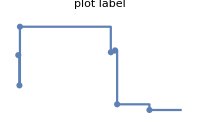

```mathematica
ClearAll[dlsp,data]
dlsp[data_]:=DateListStepPlot[data,Right,
Mesh->Full,
ImageSize->{200,130},
PlotRange->{All,{0,100}},
PlotLabel->"plot label",
Frame->{{Automatic,None},{Automatic,None}},
FrameLabel->{"Time","Reading"},
GridLines->Automatic,GridLinesStyle->Dotted];

dlsp[readingsDS[All,{"Timestamp","reading"}]]
```

```mathematica
ClearAll[outerRF,items]
outerRF[bpW_,rsMult_,w_,h_,frmTF_,items_List]:=Rasterize[
Framed[
Grid[items],
Alignment->Center,
ImageSize->{wPX[bpW],hPX[bpW,w,h]},
FrameMargins->{{0,0},{0,0}},
ContentPadding->False,
RoundingRadius->0,
FrameStyle->If[frmTF,Red,White]
],
ImageSize->{wPX[bpW],hPX[bpW,w,h]},
RasterSize->rsMult*bpW
]
items={{
ag[readingsDS[First,"reading"]],
grd[readingsDS,5],
dlsp[readingsDS[All,{"Timestamp","reading"}]]
}};
outerRF[72*7.5,3,40,10,False,items]
```

-Graphics-

```mathematica
ClearAll[args,func,funcWid,frmt,params]
args={
"reading"->"Integer",
"rows"->"Integer"
};
funcWid[dbID_]:=Function[
(*dbID="FP1rDZCv";*)
bpW=72*7.5;
w=40;
h=11;
rsMult=3;

readings=Databin[dbID,All];
readingsDB=DatabinAdd[readings,<|"reading"->#reading|>];
(*readingsDS=Dataset[readingsDB][Reverse,(SortBy[#,"Timestamp"]&)];*)
readingsDS=Dataset[readingsDB][ReverseSortBy[#1,"AbsoluteTime"]&,{"Timestamp","reading"}];

items={{
ag[readingsDS[First,"reading"]],
grd[readingsDS,#rows],
dlsp[readingsDS[All,{"Timestamp","reading"}]]
}};

outerRF[bpW,rsMult,w,h,False,items]
];
frmt="SVG"

params=<|
"reading"->53,
"rows"->6
|>;
makeAPI[args,funcWid["FP1rDZCv"],frmt][params]
```

SVG

-Graphics-

```mathematica
ClearAll[endPoint,funcName,permit]
endPoint="live-coding";
funcName="gauge-grid";
permit="Public";

makeCD[args, funcWid["FP1rDZCv"],frmt,endPoint,funcName,permit]
```

CloudObject[https://www.wolframcloud.com/obj/mitch/live-coding/gauge-grid]

```mathematica
url=URLBuild[makeCD[args, funcWid["FP1rDZCv"],frmt,endPoint,funcName,permit],params]
session=StartWebSession["Chrome"];
WebExecute[session,{"OpenPage"->url}];
```

https://www.wolframcloud.com/obj/mitch/live-coding/gauge-grid?reading=53&rows=6

## Upcoming sessions

- Add NodeJS (+ Express) to the mix
- Introducing global state management of API requests and responses in React
- User managment
- Security
- Encryption
- AWS serverless (NodeJS)
- Sockets between React/Node and WC
- Making WC read, write, listen, and speak